# Clase G - Mediciones

## Dump

Pruebas:

- Polarizacion
- Ganancia de tension
- Sensibilidad
- Potencia de salida
- Ancho de banda: a 100mV. Barro hasta ver arriba y abajo cuando cae en 3dB, con grador y oscilo
- Slew rate: le meto una cuadrada de 500mV
- Impedancia de entrada: frecs 100, 1k, 10k. Nah, sin carga, 500mV
- Impedancia de salida: Ver con oscilo como baja con carga conocida. foto
- Distorsion: a 100, 1k, 10k, a 1w y 100w. Lo tengo que traducir a dB relativo 
- Intermodulacion: ver el efecto, no se bien como se mide. Meterle frecs de 1k y 1k3Hz	
- Rechazo de riple

```mathematica
20/8.
```

2.5

```mathematica
0.3 8
```

2.4

```mathematica
18.7/0.22
```

85.

```mathematica
20/Sqrt[2]/8.
```

1.76777

## Pasos para hoy

## General

```mathematica
SetDirectory["C:\\CUBASE\\Test proj\\Audio"];
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Needs["SyntaxExtensions`"];
```

```mathematica
potAInputPico[pot_]:=Sqrt[2]/40 potAOutputPico[pot]
potAOutputRMS[pot_]:=Sqrt[pot 8]
potAOutputPico[pot_]:=potAOutputRMS[pot]*Sqrt[2]
vpico[db_]:=1.5 10^(db/20)
vdb[pico_]:=-3.52183+8.68589 Log[pico]
```

```mathematica
dbAmp[l_List]:=20 Log10[l]//alignMax;
dbAmp[l_]:=20 Log10[l];
```

```mathematica
alignMax[l_]:=l-Max[l];
```

```mathematica
audioTake[aud_, l_] := Audio@Sound`SoundTake[Sound`AudioToSound[aud], l]
```

```mathematica
dbToPow[l_]:=10^(l/10);
powToDb[l_]:=10 Log10[l]
totalDbPow=dbToPow/*Total/*powToDb;
dbToPercentage[d_]:=UnitConvert[dbToPow[d], "Percent"]
```

## Polarizacion

El multiplicador de Vbe se coloca en la tension que genera una corriente de 200mA, medida a traves de la caida por la resistencia de emisor

```mathematica
0.0095/0.22
```

0.0431818

La salida sin entrada es de 4mV

## Ganancia

A entrada de 200mV pico pico de entrada. Salida, 4.96V pico pico, 195Hz

```mathematica
ganancia195=4.96/0.2;
```

A entrada de 206mV pico pico de entrada. Salida, 4.96V pico pico, 195Hz

```mathematica
ganancia1k=4.96/0.206;
```

```mathematica
ganancia1k
```

24.0777

```mathematica
40/Sqrt[2.]
```

28.2843

## Resistencia de entrada

Todas a 100mV pico

### A 100Hz

14kOhms.

### A 1kHz

14kOhms.

### A 10kHz

10kOhms.

## Resistencia de salida

Todas a 100mV pico

```mathematica
8/(8+rout)==r
```

8/(8+rout)==r

### A 100Hz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.68V

### A 1kHz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.44V

### A 10kHz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.36

## Ancho de banda

El ancho de banda medido a 3dB va de 6.6Hz hasta 225kHz. 
La senial de salida era de 2.12V a la salida, o entrada de 85mV

## Slew Rate

## THD

```mathematica
CopyFile["Audio 01_41.wav",FileNameJoin[{NotebookDirectory[],"thd-2mW.wav"}]];
```

### Versión usando built-ins

```mathematica
getIntervals[aud_, pad_]:=AudioIntervals[aud,#ModifiedKullbackLeibler<0.05&,1]/.{b_Real,e_Real}:>{b+pad, e-pad}
octaveStep[freqs_List]:=Nearest[octaveStepCandidates,Mean@Differences[Log2@freqs], 1]//First;
baseFreq[freqs_List, step_]:=MapIndexed[{fr,ind}↦With[{in=First[ind]-1},fr 2^-(in step)],freqs]//Mean//Round[#, 5]&
octaveStepCandidates={1, 1/3};
cleanupFreqs[freqs_]:=With[{st=octaveStep[freqs]},baseFreq[freqs, st] 2^(st Range[0, Length@freqs-1])]
window[l_, w_]:=winOfLen[w, Length@l]l
winOfLen[w_, n_Integer?Positive]:=w@Subdivide[-0.5, 0.5, n+1][[2;;-2]]
```

Ahora a calcular la distorsión

```mathematica
Clear[getHarmonic, getSpec, getHarmonics];
getSpec[saud_Audio]:=TimeSeries[20 Log10@Abs@Fourier[window[AudioData[saud], BlackmanWindow], FourierParameters->{1, -1}]//alignMax,{0., saud~AudioMeasurements~"SampleRate"}];
getHarmonic[ts_,baseFreq_, n_, pad_:0.2]:=With[{freqCenter=baseFreq (n+1)},
	Max@TimeSeriesWindow[ts,  freqCenter+pad baseFreq {-1, 1}]/;
		freqCenter<Quotient[ts["LastTime"],2]];
getHarmonic[ts_, baseFreq_, n_, pad_:0.2]:=Nothing;
getHarmonics[ts_, baseFreq_, nmax_, pad_:0.2]:=getHarmonic[ts, baseFreq, #, pad]&/@Range@nmax;
```

```mathematica
Clear[processThd];
processThd[freq_, aud_, num_:10]/;freq>AudioMeasurements[aud,"SampleRate"]/4:=Nothing
processThd[freq_, aud_, num_:10]:=Quantity[freq,"Hertz"]->Let[
	{ts, getSpec[aud]},
	{harms, getHarmonics[ts, freq, num]},
	<|"THD"->dbToPercentage@totalDbPow@harms, "Harmonics"->dbToPercentage/@harms|>
	]
```

```mathematica
removeAudioSilences[aud_, thr_:0.01]:=AudioDelete[aud,AudioIntervals[aud,#RMSAmplitude<thr&]]
```

```mathematica
Clear[getThd];
getThd[aud_Audio, silenceThresh_:0.02]:=Let[
	{noSilAud, removeAudioSilences[aud, silenceThresh]},
	{sr, noSilAud~AudioMeasurements~"SampleRate"},
	{auds, audioTake[noSilAud,#]&/@getIntervals[noSilAud, 0.02]},
	{freqs, AudioMeasurements[auds,"SpectralCentroid"]//cleanupFreqs},
	{aufrec,AssociationThread[freqs, auds]},
	
	Dataset@Association@KeyValueMap[processThd, aufrec]
	]
getThd[fname_String]:=With[{aud=Import[fname]}, getThd@aud/;AudioQ@aud];
```

### General

#### Barrido en frecuencia

Necesito código que tome un Audio, que arranca y termina con silencio o ruidito (y quizá con algún valor de ayuda semiautomático), lo seccione en las partes según frecuencia, y devuelva la association de <| frec -> <| thd -> , by harmonic -> {} |>|>

La frecuencia la puedo meter a mano somehow. Not sure.

Las principales tareas son las de recortar principio y final y seccionar por frecuencia

##### Recortar principio y final

Puedo tomar un moving average de la potencia

```mathematica
sr=aud~AudioMeasurements~"SampleRate"
```

48000

```mathematica
wlen=2^13;woffset=2^10;
sp=Abs@SpectrogramArray[aud, wlen,woffset, BlackmanWindow][[All,;;wlen~Quotient~2]]//Map[GaussianFilter[#,3]&];
```

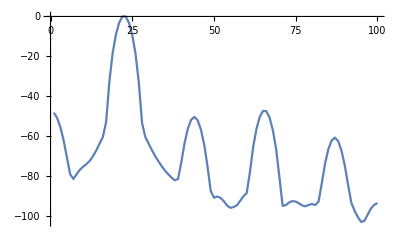

```mathematica
ListLinePlot[sp//#[[5,;;100]]&//dbAmp, PlotRange->Full]
```

```mathematica
localMax=(Sign@Differences[#]~SequencePosition~{1, -1}//Map[Mean]//N//ReplaceAll[i_?NumericQ/;i<20/48000 wlen->Nothing])&/@sp;
```

```mathematica
Clear[cleanAndCheck];
cleanAndCheck[w_List]:=With[{res=w~MedianFilter~10~GaussianFilter~5},res/;AllTrue[Differences@res,NonNegative]]
_cleanAndCheck:=Throw["Bad check"]
```

```mathematica
localMaxWeights=Function[{pow, maxs},First@MaximalBy[maxs,Interpolation[pow]]]@@@Transpose@{sp, localMax};
cleanLocalMaxWeights=cleanAndCheck[localMaxWeights];
```

```mathematica
Clear[buildSections];
buildSections[{},{}]:={};
buildSections[{}, {e_}]:={{1, e}};
buildSections[{b_}, {}]:={{b, -1}};
buildSections[{b_,rb___}, {e_,re___}]/;e<b:=buildSections[{1,b,  rb}, {e, re}];
buildSections[{bb___, lb_}, {be___,le_}]/;le<lb &&Positive[le]:=buildSections[{bb, lb}, {be, le, -1}];
buildSections[bl_List, be_List]/;Length@bl==Length@be:=With[{res=Transpose@{bl, be}},res/;OrderedQ[Flatten@res//DeleteCases[-1]]]
_buildSections:=Null/;(Throw["Bad buildSections"];False)
```

```mathematica
sects=Let[
{indx,Boole@Map[#<1&,Differences@cleanLocalMaxWeights]},
{ends,SequencePosition[indx,{1,0}][[All,1]]},
{begs,SequencePosition[indx,{0,1}][[All,2]]},
buildSections[begs, ends]
];
```

```mathematica
sampleToFreq[sr_,wlen_][sfreq_]:=sr/wlen sfreq
```

```mathematica
freqs=Take[cleanLocalMaxWeights,#]&/@sects//Map[Mean]//sampleToFreq[sr, wlen];
```

```mathematica
freqs
```

{125.977,254.871,506.83,1004.88,2000.98,3981.45,7948.24,15852.5}

```mathematica
Differences@Log10@freqs//Mean
```

0.299972

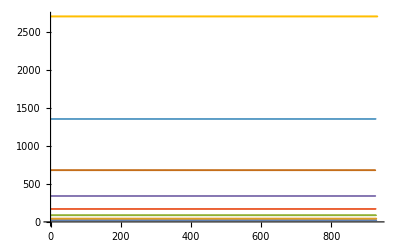

```mathematica
ListPlot[Take[cleanLocalMaxWeights,#]&/@sects]
```

```mathematica
Take[]
```

#### Barrido en amplitud

### A 2mW

```mathematica
res2mw=getThd["thd-2mW.wav"];
```

```mathematica
aud=Import["thd-2mW.wav"];
```

```mathematica
res2mw
```

Dataset[<>]

```mathematica
dat=AudioData[Import["Audio 01_31.wav"]][[1]];
```

Import::nffil: File not found during Import.

AudioData::audio: Expecting an audio object instead of $Failed.

```mathematica
dat=dat~Drop~Round[sr 3.719];
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,178512].

```mathematica
freqs={125,250,500,1000,2000,4000,8000};
samples=Range[1,Length@dat,Round[10 sr]][[2;;8]];
```

Part::take: Cannot take positions 2 through 8 in {1}.

```mathematica
dats=samples//Map[{#-10,#+10}&]//Flatten//Prepend[1]//Partition[#,2]&//Map[Take[dat,#]&];
```

Part::pkspec1: The expression {-10+2;;8,10+2;;8} cannot be used as a part specification.

Part::pkspec1: The expression {{-9},{11}} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[Drop[$Failed,178512],{{-9},{11}}].

```mathematica
Spectrogram[dat, 512,256,SampleRate->sr, FrameTicks->{Range[0,80,5], Automatic}]
```

Spectrogram::data: Drop[$Failed,178512] is not a real-valued vector.

Spectrogram[Drop[$Failed,178512],512,256,SampleRate→48000,FrameTicks→{{0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80},Automatic}]

```mathematica
Length@samples
```

2

```mathematica
fs=TimeSeries[Abs@Fourier[#], {0, 48000}]&/@dats;
```

Fourier::fftl: Argument $Failed is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument Take[Drop[$Failed,178512],{{-9},{11}}] is not a non-empty list or rectangular array of numeric quantities.

Part::pkspec1: The expression TimeSeries[Abs[Fourier[Take[Drop[$Failed,178512],{{-9},{11}}]]],{0,48000}] cannot be used as a part specification.

```mathematica
ListLinePlot[dat[[samples[[10]]-20;;samples[[10]]+20]]]
```

Part::partw: Part 10 of {1}⟦2;;8⟧ does not exist.

Part::take: Cannot take positions 2 through 8 in {1}.

Part::partw: Part 10 of {1}⟦2;;8⟧ does not exist.

Part::take: Cannot take positions 2 through 8 in {1}.

Part::partw: Part 10 of {1}⟦2;;8⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 8 in {1}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::span: -20+{1}⟦2;;8⟧⟦10⟧;;20+{1}⟦2;;8⟧⟦10⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

ListLinePlot::lpn: Drop[$Failed,178512]⟦-20+{1}⟦2;;8⟧⟦10⟧;;20+{1}⟦2;;8⟧⟦10⟧⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[Drop[$Failed,178512]⟦-20+{1}⟦2;;8⟧⟦10⟧;;20+{1}⟦2;;8⟧⟦10⟧⟧]

```mathematica
TabView
```

TabView

```mathematica
TabView[Quantity[freqs[[;;3]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 2000}]//alignMax, PlotRange->Full]&/@fs[[;;3]])//Thread]
```

Part::pkspec1: The expression TimeSeries[Abs[Fourier[Take[Drop[$Failed,178512],{{-9},{11}}]]],{0,48000}] cannot be used as a part specification.

Part::take: Cannot take positions 1 through 3 in TimeSeries[Abs[Fourier[$Failed]],{0,48000}]⟦TimeSeries[Abs[Fourier[Take[Drop[$Failed,178512],{{-9},{11}}]]],{0,48000}]⟧.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[Drop[$Failed,178512],{{-9},{11}}].

Fourier::fftl: Argument Take[Drop[$Failed,178512],{{-9},{11}}] is not a non-empty list or rectangular array of numeric quantities.

Part::pkspec1: The expression TimeSeries[Abs[Fourier[Take[Drop[$Failed,178512],{{-9},{11}}]]],{0,48000}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: alignMax[8.68589 Log[TimeSeriesWindow[TimeSeries[Abs[Fourier[«1»]],{0.,48000.}]⟦TimeSeries[Abs[Fourier[«1»]],{0,48000}]⟧,{0.,2000.}]]] is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: alignMax[8.68589 Log[TimeSeriesWindow[1.;;3.,{0.,2000.}]]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

123

```mathematica
TabView[Quantity[freqs[[4;;]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 24000}]//alignMax, PlotRange->Full]&/@fs[[4;;]])//Thread]
```

Part::take: Cannot take positions 4 through -1 in TimeSeries[Abs[Fourier[$Failed]],{0,48000}]⟦TimeSeries[Abs[Fourier[Take[Drop[$Failed,178512],{{-9},{11}}]]],{0,48000}]⟧.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[Drop[$Failed,178512],{{-9},{11}}].

Fourier::fftl: Argument Take[Drop[$Failed,178512],{{-9},{11}}] is not a non-empty list or rectangular array of numeric quantities.

Part::pkspec1: The expression TimeSeries[Abs[Fourier[Take[Drop[$Failed,178512],{{-9},{11}}]]],{0,48000}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: alignMax[8.68589 Log[TimeSeriesWindow[TimeSeries[Abs[Fourier[«1»]],{0.,48000.}]⟦TimeSeries[Abs[Fourier[«1»]],{0,48000}]⟧,{0.,24000.}]]] is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: alignMax[8.68589 Log[TimeSeriesWindow[4.;;All,{0.,24000.}]]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

1234

### A 1W

#### Generate

```mathematica
pot=1;
vrms=Sqrt[pot 8.];
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.141421

```mathematica
potAInputPico[vin]
```

0.053183

```mathematica
vdb[vin]
```

-20.5115

#### Analyse

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
res10w=getThd["thd-10w.wav"];
```

$Aborted

```mathematica
res10w
```

```mathematica
res1w
```

Dataset[<>]

### A 10W

#### Generate

```mathematica
pot=10;
vrms=Sqrt[pot 8.];
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.447214

```mathematica
vvpico
```

12.6491

```mathematica
potAInputPico[vin]
```

0.0945742

```mathematica
vdb[vin]
```

-10.5115

#### Analyse

```mathematica
res10w=getThd["thd-10w.wav"];
```

```mathematica
res10w
```

Dataset[<>]

### A 100W

#### Generate

```mathematica
vrms=1/8.;
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.00625

```mathematica
potAInputPico[vin]
```

0.0111803

```mathematica
vdb[vin]
```

-47.6042

#### Analyse

```mathematica
res100w=getThd["thd-100w.wav"];
```

$Aborted

```mathematica
res100w
```

## Intermodulacion

```mathematica
aud=Import["C:\\CUBASE\\Test proj\\Audio\\Audio 01_19.wav"];
```

Import::nffil: File not found during Import.

```mathematica
dat=AudioData[aud][[1]];
```

AudioData::audio: Expecting an audio object instead of $Failed.

```mathematica
f=TimeSeries[Abs@Fourier[dat], {0, 48000}];
```

Fourier::fftl: Argument $Failed is not a non-empty list or rectangular array of numeric quantities.

```mathematica
ListLinePlot[20 Log10@TimeSeriesWindow[f, {0, 400}]//alignMax, PlotRange->Full]
```

ListLinePlot::lpn: 0. is not a list of numbers or pairs of numbers.

ListLinePlot[0,PlotRange→Full]

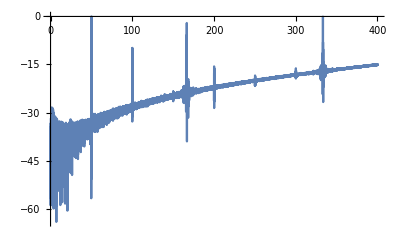

O sea, 0dB aca es aprox 1.5V pico de salida. Cada 20dB es dividir por 10 supongo.

```mathematica
1.5 10^(db/20)==vpico//Solve
```

{{db→-3.52183+8.68589 Log[vpico]}}

```mathematica
potAOutputPico[100.]
```

40.

```mathematica
potAInputPico[1]//vdb
```

-20.5115

```mathematica
potAInputPico[1]//N
```

0.141421

```mathematica
8/0.3
```

26.6667

```mathematica
70./1000
```

0.07

```mathematica
0.07^2 30
```

0.147

```mathematica
Audio
```

Audio

```mathematica
Play[0.05 Sin[2 Pi 440 t], {t, 0, 20}, PlayRange->{-1,1}, SampleRate->48000, SampleDepth->24]
```

-Graphics-

```mathematica
$DefaultAudioInputDevice
```

$DefaultAudioInputDevice

```mathematica
ac=AudioCapture[SampleRate->48000];
```

```mathematica
AudioGenerator[{"Sin", 1000}, 10, "Real", SampleRate->48000]
```

```mathematica
ac
```

AudioCapture[SampleRate→48000]

```mathematica
Import["
```

```mathematica
aud=;
```

```mathematica
Head[aud]
```

AudioClass→AudioFile

```mathematica
dat=AudioData[aud][[1]];
```

AudioData::audio: Expecting an audio object instead of (AudioClass→AudioFile)[].

```mathematica
dat//Dimensions
```

{1}

```mathematica
Histogram[dat]
```

Histogram::ldata: (AudioClass→AudioFile)[] is not a valid dataset or list of datasets.

Histogram[(AudioClass→AudioFile)[]]

```mathematica
MinMax[dat]
```

{(AudioClass→AudioFile)[],(AudioClass→AudioFile)[]}

```mathematica
fou=TimeSeries[Abs[Fourier[dat, FourierParameters->{1,-1}]], {0, 48000.}];
```

Fourier::fftl: Argument (AudioClass→AudioFile)[] is not a non-empty list or rectangular array of numeric quantities.

```mathematica
ListLinePlot[TimeSeriesWindow[ fou, {0, 5000}], PlotRange->Full]
```

Fourier::fftl: Argument (AudioClass→AudioFile)[] is not a non-empty list or rectangular array of numeric quantities.

ListLinePlot::lpn: TimeSeriesWindow[TimeSeries[Abs[Fourier[(AudioClass→AudioFile)[DynamicModule[{Set[«2»],Audio`AudioObjects`audioID,Set[«2»],Audio`AudioObjects`newAudio},,Initialization:>Set[«2»],DynamicModuleValues:>{},Deinitialization:>CompoundExpression[«2»],UnsavedVariables:>{«2»}]],FourierParameters→{1.,-1.}]],{0.,48000.}],{0.,5000.}] is not a list of numbers or pairs of numbers.

Fourier::fftl: Argument (AudioClass→AudioFile)[] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

ListLinePlot::lpn: TimeSeriesWindow[TimeSeries[Abs[Fourier[(AudioClass→AudioFile)[DynamicModule[{Set[«2»],Audio`AudioObjects`audioID,Set[«2»],Audio`AudioObjects`newAudio},,Initialization:>Set[«2»],DynamicModuleValues:>{},Deinitialization:>CompoundExpression[«2»],UnsavedVariables:>{«2»}]],FourierParameters→{1.,-1.}]],{0.,48000.}],{0.,5000.}] is not a list of numbers or pairs of numbers.

ListLinePlot[TimeSeriesWindow[TimeSeries[Abs[Fourier[(AudioClass→AudioFile)[],FourierParameters→{1,-1}]],{0,48000.}],{0,5000}],PlotRange→Full]

```mathematica
ListLinePlot[fou]
```

Fourier::fftl: Argument (AudioClass→AudioFile)[] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

ListLinePlot::lpn: TimeSeries[Abs[Fourier[(AudioClass→AudioFile)[],FourierParameters→{1.,-1.}]],{0.,48000.}] is not a list of numbers or pairs of numbers.

ListLinePlot[TimeSeries[Abs[Fourier[(AudioClass→AudioFile)[],FourierParameters→{1,-1}]],{0,48000.}]]

```mathematica
ListLinePlot[, PlotRange->Full, DataRange->{0, 48000}]
```

ListLinePlot::lpn: Null is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Null,PlotRange→Full,DataRange→{0,48000}]

## Yeah

```mathematica
dat=Import["Audio 01_25.wav","WAV"]//AudioData//First;
```

Import::nffil: File not found during Import.

AudioData::audio: Expecting an audio object instead of $Failed.

```mathematica
ListLinePlot[20 Log10@TimeSeriesWindow[f, {0, 4000}]//alignMax, PlotRange->Full]
```

ListLinePlot::lpn: 0. is not a list of numbers or pairs of numbers.

ListLinePlot[0,PlotRange→Full]

```mathematica
dat
```

$Failed

```mathematica
Directory[]
```

/mnt/froot/home/rui

```mathematica
dat//Dimensions
```

{}